```mathematica
mnist=ResourceData["MNIST","TrainingData"];
mnistTest=ResourceData["MNIST","TestData"];
group[i_]:=group[i]=Select[mnist,#[[2]]==i&][[All,1]]
trainSize[i_]:=trainSize[i]=Length[group[i]]
groupTest[i_]:=groupTest[i]=Select[mnistTest,#[[2]]==i&][[All,1]]
testSize[i_]:=testSize[i]=Length[groupTest[i]]
vec[img_]:=1-Flatten[ImageData[img]]
```

```mathematica
data=vec/@mnist[[All,1]];
labels=mnist[[All,2]];
testData=vec/@mnistTest[[All,1]];
testLabels=mnistTest[[All,2]];
nTest=Length[testLabels];
classes=DeleteDuplicates[labels];
nClasses=Length[classes];
pos=AssociationThread[classes->Range[nClasses]];
```

```mathematica
dist[vec_]:=Block[{z=vec,a},Do[a=W[j].z+b[j];
z=Ramp[a],{j,L+1}];
Exp[a]/Total[Exp[a]]]
pred[vec_]:=Block[{y=dist[vec]},classes[[FirstPosition[y,Max[y]][[1]]]]]
batchDist[vecs_]:=Block[{Z=Transpose[vecs],A},Do[A=W[j].Z+b[j];Z=Ramp[A],{j,L+1}];Z=Exp[Transpose[A]];Z/(Total/@Z)]
batchPred[vecs_]:=Block[{Y=batchDist[vecs]},classes[[FirstPosition[#,Max[#]][[1]]&/@Y]]]
```

```mathematica
epochs=100;
updateFrequency=1;
lr=10^-1;
initRange=1/2;
{n,d0}=Dimensions[data];
hiddenDims={256,256};
allDims=Join[{d0},hiddenDims,{nClasses}];
L=Length[hiddenDims];
Do[scale=√(2.0/allDims[[l]]);
W[l]=RandomVariate[NormalDistribution[],{allDims[[l+1]],allDims[[l]]}]scale;
b[l]=ConstantArray[0,allDims[[l+1]]],{l,L+1}];
trainPreds=batchPred[data];
matches=MapThread[Equal,{trainPreds,labels}];
acc[0]=N[Count[matches,True]/n];
testPreds=batchPred[testData];
testMatches=MapThread[Equal,{testPreds,testLabels}];
accTest[0]=N[Count[testMatches,True]/nTest];
```

```mathematica
Monitor[Do[batch=data;
rVec=pos/@labels;
Z[0]=Transpose[batch];
Do[A[j]=W[j].Z[j-1]+b[j];
Z[j]=Ramp[A[j]],{j,L}];
A[L+1]=W[L+1].Z[L]+b[L+1];
Y=Exp[Transpose[A[L+1]]];
Y=#/Total[#]&/@Y;
labelMat=UnitVector[nClasses,#]&/@rVec;
e[L+1]=Y-labelMat;
Do[e[j]=e[j+1].W[j+1]Transpose[UnitStep[Z[j]-$MachineEpsilon]],{j,L,1,-1}];
Do[gradQW[j]=Transpose[Z[j-1].e[j]];
gradQb[j]=Total[e[j]],{j,L+1}];
loss[m-1]=-Total[Log[Y]labelMat,2];
Print[loss[m-1]];
Do[W[j]-=lr gradQW[j]/n;
b[j]-=lr gradQb[j]/n,{j,L+1}];
If[Mod[m,updateFrequency]==0,trainPreds=batchPred[data];
matches=MapThread[Equal,{trainPreds,labels}];
acc[m]=N[Count[matches,True]/n];
testPreds=batchPred[testData];
testMatches=MapThread[Equal,{testPreds,testLabels}];
accTest[m]=N[Count[testMatches,True]/nTest]],{m,epochs}],m]
```

148214.

134850.

127772.

121647.

115863.

110245.

104747.

99379.2

94175.2

89179.7

84433.4

79967.6

75804.3

71951.3

68407.3

65161.7

62198.5

59497.

57034.9

54790.2

52742.

50870.6

49157.1

47585.7

46142.1

44812.

43584.6

42449.5

41397.8

40420.9

39511.6

38663.7

37871.5

37129.5

36433.3

35779.3

35163.6

34583.1

34035.1

33516.8

33026.

32560.6

32118.8

31698.8

31299.3

30918.6

30555.5

30208.9

29877.6

29560.6

29257.

28965.9

28686.5

28418.2

28160.1

27911.8

27672.8

27442.3

27220.

27005.4

26798.1

26597.7

26403.8

26216.1

26034.5

25858.4

25687.6

25521.9

25361.

25204.8

25052.9

24905.2

24761.4

24621.4

24485.

24352.1

24222.5

24096.1

23972.7

23852.3

23734.7

23619.8

23507.4

23397.7

23290.4

23185.4

23082.6

22982.

22883.5

22786.9

22692.2

22599.4

22508.3

22419.

22331.3

22245.1

22160.6

22077.5

21995.9

21915.7

{{0,0.103117,0.102},{1,0.171683,0.1705},{2,0.268483,0.2663},{3,0.395233,0.3983},{4,0.507683,0.5155},{5,0.575083,0.5773},{6,0.61545,0.6227},{7,0.647283,0.6516},{8,0.671517,0.6774},{9,0.69175,0.7007},{10,0.709167,0.7189},{11,0.723817,0.7358},{12,0.737983,0.7488},{13,0.750167,0.7627},{14,0.761467,0.7722},{15,0.77235,0.7828},{16,0.781233,0.7937},{17,0.7891,0.8029},{18,0.796683,0.8098},{19,0.803683,0.8158},{20,0.809317,0.8207},{21,0.815083,0.8255},{22,0.820017,0.8303},{23,0.824433,0.8351},{24,0.82835,0.839},{25,0.832033,0.8427},{26,0.835117,0.845},{27,0.838183,0.8477},{28,0.841267,0.8505},{29,0.844067,0.8536},{30,0.846633,0.8552},{31,0.849333,0.8573},{32,0.85165,0.8594},{33,0.8534,0.8608},{34,0.85515,0.8632},{35,0.85705,0.8648},{36,0.8592,0.8662},{37,0.860517,0.8677},{38,0.86235,0.8692},{39,0.863683,0.8706},{40,0.8653,0.8719},{41,0.866333,0.8734},{42,0.867767,0.8747},{43,0.868983,0.8763},{44,0.869817,0.8771},{45,0.87085,0.8785},{46,0.872033,0.8798},{47,0.872833,0.8806},{48,0.873733,0.8819},{49,0.874383,0.8829},{50,0.87505,0.8835},{51,0.875983,0.8842},{52,0.876767,0.8849},{53,0.87775,0.8855},{54,0.878583,0.8867},{55,0.879383,0.8877},{56,0.880367,0.8885},{57,0.881117,0.8901},{58,0.88185,0.8907},{59,0.8823,0.891},{60,0.882867,0.8917},{61,0.883733,0.8925},{62,0.884567,0.8933},{63,0.884967,0.8941},{64,0.885533,0.8946},{65,0.886183,0.8953},{66,0.886767,0.8959},{67,0.887333,0.8964},{68,0.88795,0.8969},{69,0.888467,0.8974},{70,0.888883,0.8977},{71,0.889467,0.898},{72,0.89005,0.8983},{73,0.890683,0.8986},{74,0.891183,0.8989},{75,0.89185,0.8995},{76,0.89225,0.8999},{77,0.892733,0.9007},{78,0.8932,0.9013},{79,0.89345,0.9012},{80,0.8938,0.9014},{81,0.894167,0.9018},{82,0.894517,0.9018},{83,0.89485,0.9023},{84,0.895267,0.9024},{85,0.895633,0.9027},{86,0.895967,0.903},{87,0.896317,0.9032},{88,0.896683,0.9034},{89,0.896983,0.9035},{90,0.897283,0.9039},{91,0.8977,0.9044},{92,0.89795,0.9048},{93,0.8982,0.905},{94,0.898483,0.9055},{95,0.898683,0.9058},{96,0.8993,0.9063},{97,0.8996,0.9066},{98,0.899917,0.9067},{99,0.900217,0.9072},{100,0.90055,0.9071}}

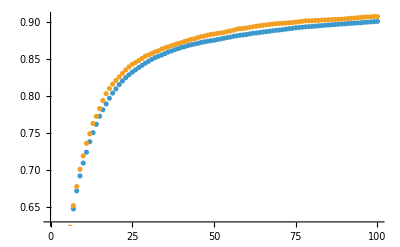

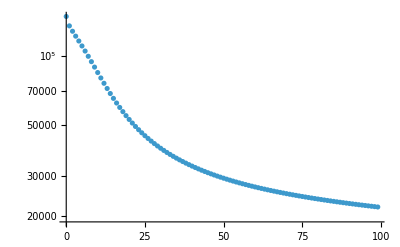

```mathematica
Table[{i,acc[i],accTest[i]},{i,0,epochs,updateFrequency}]
ListPlot[{Table[{i,acc[i]},{i,0,epochs,updateFrequency}],
Table[{i,accTest[i]},{i,0,epochs,updateFrequency}]}]
ListLogPlot[Table[{i,loss[i]},{i,0,epochs,updateFrequency}]]
```